```mathematica
Public assessment of reputations
```

```mathematica
Global Conditions
```

Conditions Global

```mathematica
Clear["Global`*"]
ϵ=(1-e1)*(1-e)+e1*e;
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/figures"];
```

```mathematica
i=0.03;
j=3;
solt=NSolve[{
0==z*(1-z)*(piz-piy),
0==Qdg*g+1-g-gy,
0==Qcg*g+1-g-gz,0≤z≤1,0≤ gy< 1,0≤ gz≤ 1}/.{e1->i,e->i,r->j},{z,gy,gz}];
{Z1,GY1,GZ1}=Last[SortBy[Evaluate[{z,gy,gz}/.sol1],First]]//.{}->Nothing
```

{1.,1.,1.}

```mathematica
0==z*(1-z)*(piz-piy),
0==Qdg*g+1-g-gy,
0==Qcg*g+1-g-gz
```

{0,1.,1.}

```mathematica
solt
```

{{gz→0.977502,gy→0.642844,z→0.960451},{gz→0.957528,gy→0.523313,z→0},{gz→0.957528,gy→0.523313,z→0},{gz→0.957528,gy→0.523313,z→0},{gz→0.957528,gy→0.523313,z→0},{gz→0.957528,gy→0.523313,z→0},{gz→0.957528,gy→0.523313,z→0},{gz→0.955646,gy→0.432842,z→0.413962}}

```mathematica
Evaluate[{z,gy,gz}/.DeleteDuplicates[SetPrecision[sol1,6]]]
```

{{0.915285,0.619884,0.958514},{0,0.539807,0.932128},{0.492309,0.462044,0.931307}}

Simple Standing

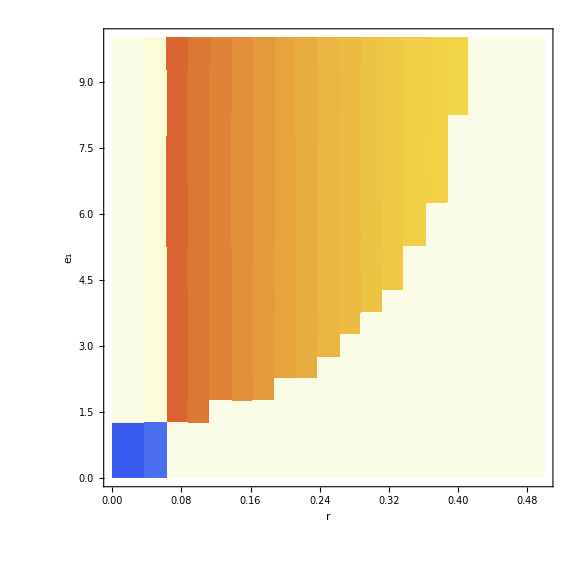

```mathematica
Simple Standing
g=(1-z)*gy+z*gz;
λ=0;
gb=(1-λ)*g;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
piy=r*gy*z;
piz=r*gz*z-g;
n=20;
coop=Array[m,{(n-1)^2,3}];
count = 1;
Do[
sol1=NSolve[{
0==z*(1-z)*(piz-piy),
0==Qdg*g+1-g-gy,
0==Qcg*g+1-g-gz,0≤z<1,0≤ gy≤ 1,0≤ gz≤ 1}/.{e1->i/(2*n),e->i/(2*n),r->10*j/n},{z,gy,gz},WorkingPrecision->50];
{Z1,GY1,GZ1}=Last[SortBy[Evaluate[{z,gy,gz}/.DeleteDuplicates[SetPrecision[sol1,6]]],First]]//.{}->Nothing;
{Z2,GY2,GZ2}=If[r*(ϵ-e)-1>0/.{e1->i/(2*n),e->i/(2*n),r->10*j/n},{1,e,ϵ}/.{e1->i/(2*n),e->i/(2*n)},{0,0.5,(ϵ-e)/2}/.{e1->i/(2*n),e->i/(2*n)}];
coop[[count]]= {i/(2*n),10*j/n,Z1*(GY1*(1-Z1)+GZ1*Z1)-Z2*(GY2*(1-Z2)+GZ2*Z2)};

(*J=D[{z*(1-z)*(piz-piy),Qdg*g+1-g-gy,Qcg*g+1-g-gz},{z,gy,gz}]*);

count=count+1;
,{i,1,n-1},{j,1,n-1}];
plt2r=ListDensityPlot[coop,ImageSize->Large,BaseStyle->{FontSize->28},PlotRange->{{0,0.5},{0,10}},PlotRangePadding->Scaled[.025],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["r"],FrameStyle->None],Framed[Style["e_1"],FrameStyle->None]},LabelStyle->Directive[FontSize->24],InterpolationOrder->0]
Export["SS_errors_v_r.pdf",plt2r];
```

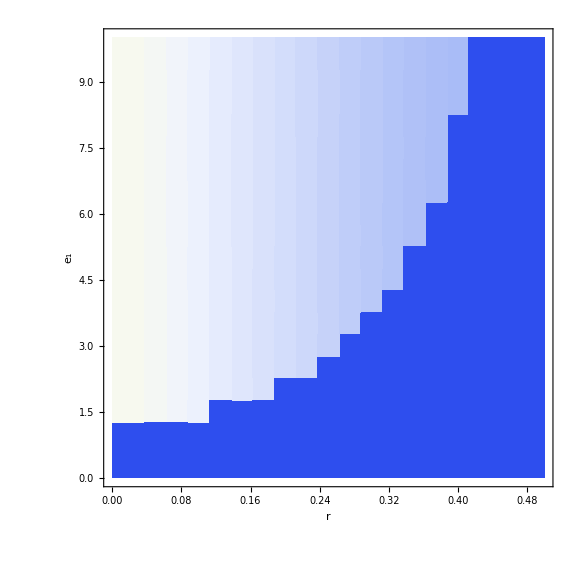

```mathematica
plt2r=ListDensityPlot[coop,ImageSize->Large,BaseStyle->{FontSize->28},PlotRange->{{0,0.5},{0,10}},PlotRangePadding->Scaled[.025],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["r"],FrameStyle->None],Framed[Style["e_1"],FrameStyle->None]},LabelStyle->Directive[FontSize->24],InterpolationOrder->0]
Export["SS_errors_v_r.pdf",plt2r];
```

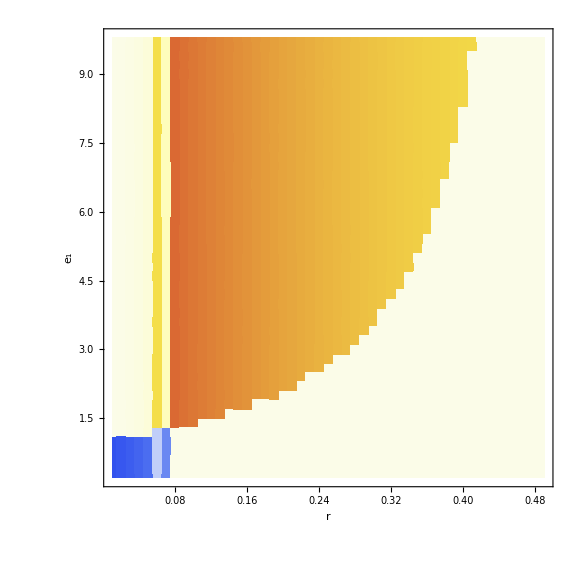

```mathematica
ListDensityPlot[coop,ImageSize->Large,BaseStyle->{FontSize->28},PlotRange->Full,PlotRangePadding->Scaled[.025],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["r"],FrameStyle->None],Framed[Style["e_1"],FrameStyle->None]},LabelStyle->Directive[FontSize->24],InterpolationOrder->0,PlotLegends->Automatic]
```

```mathematica
Export["SS_public_error.pdf",plt2r];
```

Simple Standing

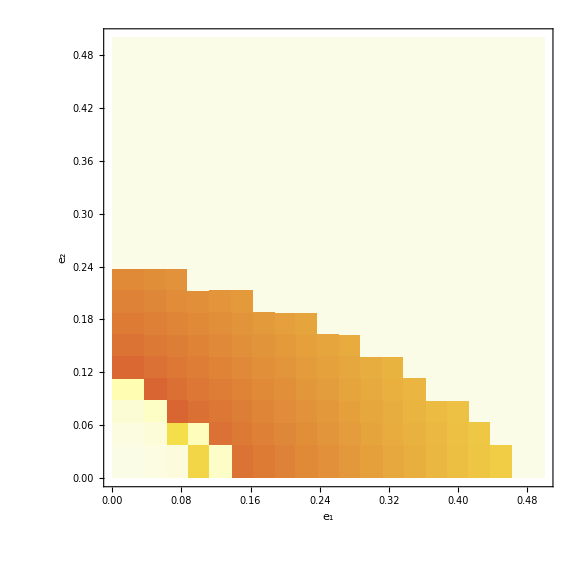

SS_e1_v_e2.pdf

```mathematica
Simple Standing
g=(1-z)*gy+z*gz;
λ=0;
gb=(1-λ)*g;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
piy=r*gy*z;
piz=r*gz*z-g;
n=20;
coop=Array[m,{(n-1)^2,3}];
count = 1;

Do[
sol1=NSolve[{
0==z*(1-z)*(piz-piy),
0==Qdg*g+1-g-gy,
0==Qcg*g+1-g-gz,0≤z≤1,0≤ gy≤ 1,0≤ gz≤ 1}/.{e1->i/(2*n),e->j/(2*n),r->2},{z,gy,gz}];
{Z1,GY1,GZ1}=Last[SortBy[Evaluate[{z,gy,gz}/.DeleteDuplicates[SetPrecision[sol1,6]]],First]]//.{}->Nothing;
{Z2,GY2,GZ2}=If[r*(ϵ-e)-1>0/.{e1->i/(2*n),e->j/(2*n),r->2},{1,e,ϵ}/.{e1->i/(2*n),e->j/(2*n),r->2},{0,0.5,(ϵ-e)/2}/.{e1->i/(2*n),e->j/(2*n),r->2}];

coop[[count]]= {i/(2*n),j/(2*n),Z1*(GY1*(1-Z1)+GZ1*Z1)-Z2*(GY2*(1-Z2)+GZ2*Z2)};
count=count+1;
,{i,1,n-1},{j,1,n-1}];
plt1=ListDensityPlot[coop,ImageSize->Large,BaseStyle->{FontSize->28},PlotRange->{{0,0.5},{0,0.5}},PlotRangePadding->Scaled[.025],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["e_1"],FrameStyle->None],Framed[Style["e_2"],FrameStyle->None]},LabelStyle->Directive[FontSize->24],InterpolationOrder->0]
Export["SS_e1_v_e2.pdf",plt1]
```

e1 e2 Simple Standing v

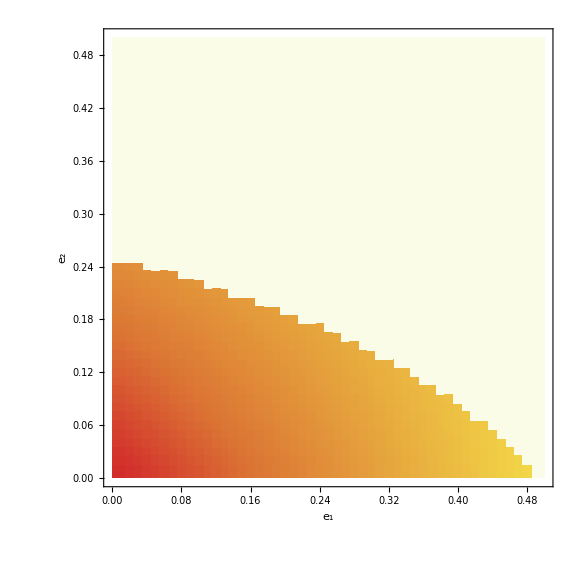

SS_e1_v_e2.pdf

```mathematica
Simple Standing e1 v e2
g=(1-z)*gy+z*gz;
λ=0;
gb=(1-λ)*g;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
piy=r*gy*z;
piz=r*gz*z-g;
n=50;
coop=Array[m,{(n-1)^2,3}];
count = 1;

Do[
c3=-(ϵ-e)*((r-1)*(ϵ-e)+r*(1-2*e))/.{e1->i/(2*n),e->j/(2*n),r->2};c2=(3*r-1)*(ϵ-e)*(1-2*e)-r*ϵ*(1-ϵ)/.{e1->i/(2*n),e->j/(2*n),r->2};c1=(2*r-1)*(e^2+ϵ*(1-2*e))-(3*r-1)*(ϵ-e)*(1-2*e)/.{e1->i/(2*n),e->j/(2*n),r->2};c0=-e*r*(1-e)/.{e1->i/(2*n),e->j/(2*n),r->2};
Δ1=18*c3*c2*c1*c0-4*c0*c2^3+(c2*c1)^2-4*c3*c1^3-27*(c3*c0)^2;
{d3,d2,d1,d0}=CoefficientList[c3*(v-1)^3+c2*(v-1)^2+c1*(v-1)+c0,v];
Δ2=18*d3*d2*d1*d0-4*d0*d2^3+(d2*d1)^2-4*d3*d1^3-27*(d3*d0)^2;
{Z1,GY1,GZ1}=If[Δ1>0&&Δ2<0,{1,e,ϵ}/.{e1->i/(2*n),e->j/(2*n),r->2},{0,0.5,(ϵ-e)/2}/.{e1->i/(2*n),e->j/(2*n),r->2}];
{Z2,GY2,GZ2}=If[r*(ϵ-e)-1>0/.{e1->i/(2*n),e->j/(2*n),r->2},{1,e,ϵ}/.{e1->i/(2*n),e->j/(2*n),r->2},{0,0.5,(ϵ-e)/2}/.{e1->i/(2*n),e->j/(2*n),r->2}];

coop[[count]]= {i/(2*n),j/(2*n),Z1*(GY1*(1-Z1)+GZ1*Z1)-Z2*(GY2*(1-Z2)+GZ2*Z2)};
count=count+1;
,{i,1,n-1},{j,1,n-1}];
plt1=ListDensityPlot[coop,ImageSize->Large,BaseStyle->{FontSize->28},PlotRange->{{0,0.5},{0,0.5}},PlotRangePadding->Scaled[.025],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["e_1"],FrameStyle->None],Framed[Style["e_2"],FrameStyle->None]},LabelStyle->Directive[FontSize->24],InterpolationOrder->0]
Export["SS_e1_v_e2.pdf",plt1]
```

```mathematica
c3=-(ϵ-e)*((r-1)*(ϵ-e)+r*(1-2*e));c2=(3*r-1)*(ϵ-e)*(1-2*e)-r*ϵ*(1-ϵ);c1=(2*r-1)*(e^2+ϵ*(1-2*e))-(3*r-1)*(ϵ-e)*(1-2*e);c0=-e*r*(1-e);
{d3,d2,d1,d0}=CoefficientList[c3*(v-1)^3+c2*(v-1)^2+c1*(v-1)+c0,v]
```

{-3 (1-e) e,-8 (1-2 e) (-e+(1-e) (1-e1)+e e1)+5 (e^2+(1-2 e) ((1-e) (1-e1)+e e1)),-3 (1-(1-e) (1-e1)-e e1) ((1-e) (1-e1)+e e1)+8 (1-2 e) (-e+(1-e) (1-e1)+e e1),(e-(1-e) (1-e1)-e e1) (3 (1-2 e)+2 (-e+(1-e) (1-e1)+e e1))}

```mathematica
Simple Standing errors v r
g=(1-z)*gy+z*gz;
λ=0;
gb=(1-λ)*g;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
piy=r*gy*z;
piz=r*gz*z-g;
n=200;
coop=Array[m,{(n-1)^2,3}];
count = 1;
Do[
c3=-(ϵ-e)*((r-1)*(ϵ-e)+r*(1-2*e));c2=(3*r-1)*(ϵ-e)*(1-2*e)-r*ϵ*(1-ϵ);c1=(2*r-1)*(e^2+ϵ*(1-2*e))-(3*r-1)*(ϵ-e)*(1-2*e);c0=-e*r*(1-e);
Δ1=18*c3*c2*c1*c0-4*c0*c2^3+(c2*c1)^2-4*c3*c1^3-27*(c3*c0)^2/.{e1->i/(2*n),e->i/(2*n),r->10*j/n};
{d0,d1,d2,d3}=CoefficientList[c3*(v-1)^3+c2*(v-1)^2+c1*(v-1)+c0,v];
Δ2=18*d3*d2*d1*d0-4*d0*d2^3+(d2*d1)^2-4*d3*d1^3-27*(d3*d0)^2/.{e1->i/(2*n),e->i/(2*n),r->10*j/n};
{Z2,GY2,GZ2}=If[r*(ϵ-e)-1>0/.{e1->i/(2*n),e->i/(2*n),r->10*j/n},{1,e,ϵ}/.{e1->i/(2*n),e->i/(2*n)},{0,0.5,(ϵ-e)/2}/.{e1->i/(2*n),e->i/(2*n)}];
{Z1,GY1,GZ1}=If[Δ1>  0,{1,e,ϵ}/.{e1->i/(2*n),e->i/(2*n),r->10*j/n},{0,0.5,(ϵ-e)/2}/.{e1->i/(2*n),e->i/(2*n),r->10*j/n}];
coop[[count]]= {i/(2*n),10*j/n,Z1*(GY1*(1-Z1)+GZ1*Z1)-Z2*(GY2*(1-Z2)+GZ2*Z2)};

(*J=D[{z*(1-z)*(piz-piy),Qdg*g+1-g-gy,Qcg*g+1-g-gz},{z,gy,gz}]*);

count=count+1;
,{i,1,n-1},{j,1,n-1}];
plt2r=ListDensityPlot[coop,ImageSize->Large,BaseStyle->{FontSize->28},PlotRange->{{0,0.5},{1,10}},PlotRangePadding->Scaled[.025],ColorFunctionScaling->False,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["e_1"],FrameStyle->None],Framed[Style["r"],FrameStyle->None]},LabelStyle->Directive[FontSize->24],InterpolationOrder->0]
Export["SS_errors_v_r.pdf",plt2r];
```

errors r Simple Standing v

-Graphics-

```mathematica
i=2;
j=1;
n=20
```

20

```mathematica
c3=-(ϵ-e)*((r-1)*(ϵ-e)+r*(1-2*e));c2=(3*r-1)*(ϵ-e)*(1-2*e)-r*ϵ*(1-ϵ);c1=(2*r-1)*(e^2+ϵ*(1-2*e))-(3*r-1)*(ϵ-e)*(1-2*e);c0=-e*r*(1-e);
Δ1=18*c3*c2*c1*c0-4*c0*c2^3+(c2*c1)^2-4*c3*c1^3-27*(c3*c0)^2/.{e1->i/(2*n),e->i/(2*n),r->10*j/n}
```

319752648225547/20480000000000000

```mathematica
Δ=18*c3*c2*c1*c0-4*c0*c2^3+(c2*c1)^2-4*c3*c1^3-27*(c3*c0)^2;
c3=-(ϵ-e)*((r-1)*(ϵ-e)+r*(1-2*e));
c2=(3*r-1)*(ϵ-e)*(1-2*e)-r*ϵ*(1-ϵ);
c1=(2*r-1)*(e^2+ϵ*(1-2*e))-(3*r-1)*(ϵ-e)*(1-2*e);
c0=-e*r*(1-e);
```

```mathematica
Solve[x==e*x+(1-e)*(1-x),x]
Solve[x==ϵ/2+(1-e)/2,x]
Solve[x==ϵ*x+(1-e)*(1-x),x]
Solve[0==R*(ϵ-e)-1,R]
```

{{x→1/2}}

{{x→1/2 (2-2 e-e1+2 e e1)}}

{{x→(-1+e)/(-1-e1+2 e e1)}}

{{R→1/((-1+2 e) (-1+e1))}}

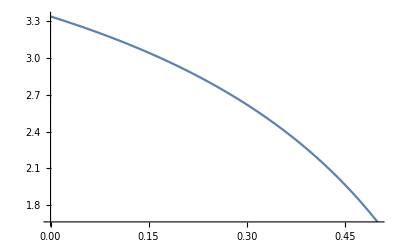

```mathematica
plt2=Plot[10*(1-3+e1*3)/(2 (-1+e1)*3),{e1,0,0.5}]
```

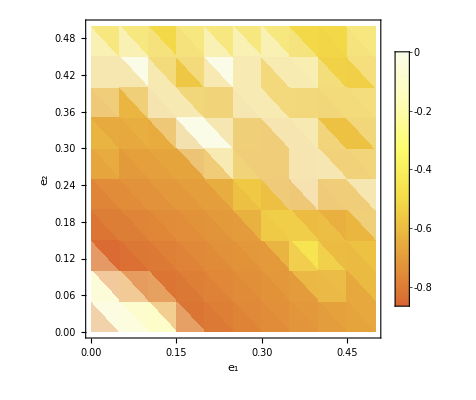

```mathematica
Show[plt1,plt2]
```

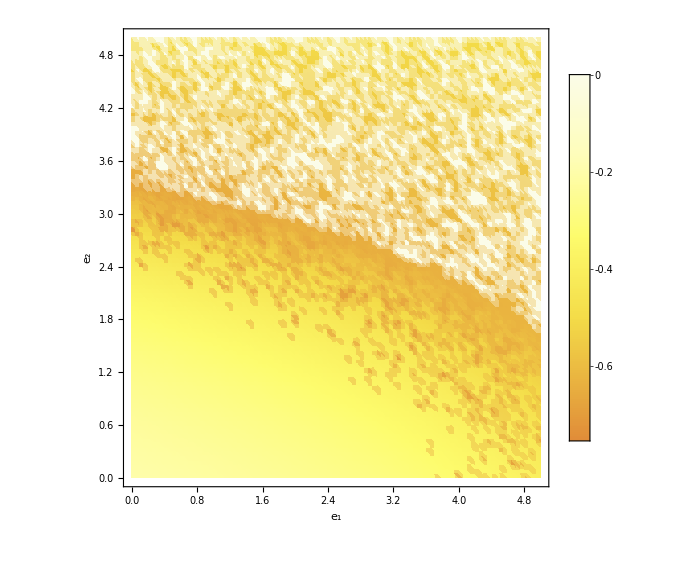

```mathematica
imageerrorSSBayes=ListDensityPlot[coop,PlotRange->Full,ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->24]]
Export["SS_public_error.pdf",imageerrorSSBayes];
```

R Simple Standing

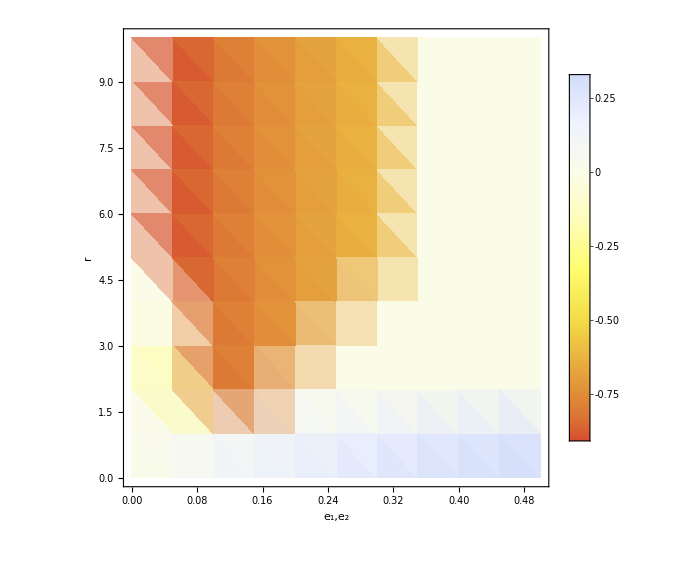

```mathematica
Simple Standing R
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
bias=0;
λ=0;
gb=(1-λ)*g;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=1;
Pdb=1;
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=1;
Qdb=1;
repsys={
gx'[t]==Qcg*g+1-g-gx[t],
gy'[t]==Qdg*g+1-g-gy[t],
gz'[t]==Qcg*g+1-g-gz[t]
};
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
Bayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg*g+1-g-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg*g+1-g-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg*g+1-g-gz[t])/.{x->x[t],y->y[t]})
};
nonBayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(ϵ*g+(1-e)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(e*g+(1-e)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(ϵ*g+(1-e)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
coopBayes=Array[m,{121,3}];
zoutBayes=Array[m,{121,3}];
coopnonBayes=Array[m,{121,3}];
zoutnonBayes=Array[m,{121,3}];
coop=Array[m,{121,3}];
zout=Array[m,{121,3}];
count = 1;
Do[
RBayes=NDSolve[Join[Evaluate[Bayessys/.{e1->i/20,e->i/20,r->j}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
RnonBayes=NDSolve[Join[Evaluate[nonBayessys/.{e1->i/20,e->i/20,r->j}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
coop[[count]]= {i/20,j,Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]]-Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]]};
count=count+1;
,{i,0,10},{j,0,10}];
imageerrorRSSBayes=ListDensityPlot[coop,PlotRange->Full,ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1,e_2","r"},LabelStyle->Directive[FontFamily->"Arial",FontSize->24]]
Export["SS_public_error_r.pdf",imageerrorRSSBayes];
```

Simple Standing

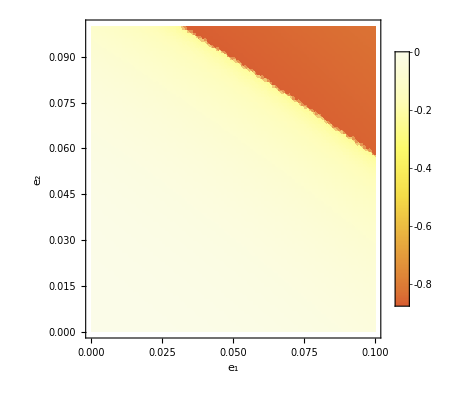

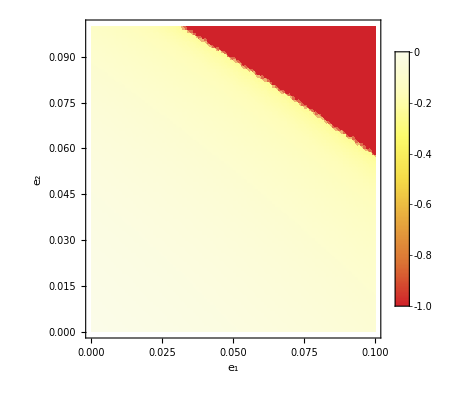

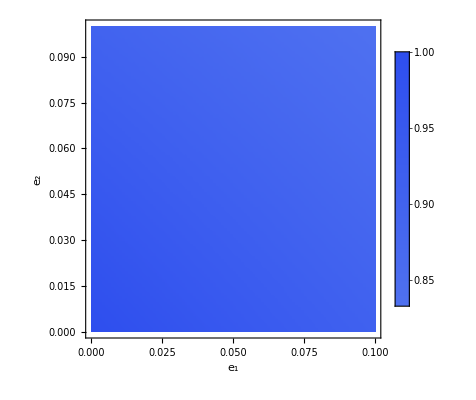

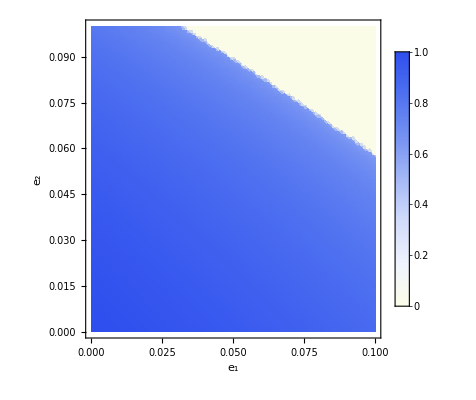

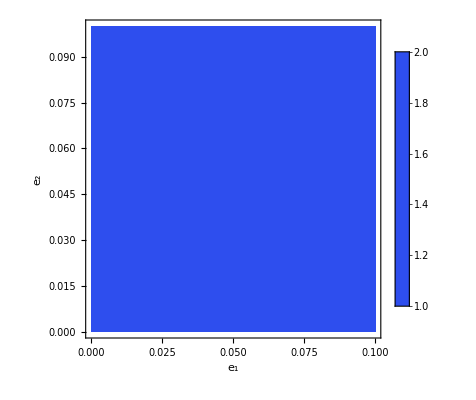

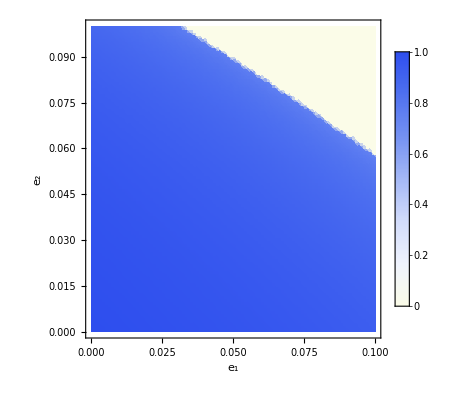

```mathematica
Simple Standing
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
bias=0;
λ=0;
gb=(1-λ)*g;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=1;
Pdb=1;
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=1;
Qdb=1;
repsys={
gx'[t]==Qcg*g+1-g-gx[t],
gy'[t]==Qdg*g+1-g-gy[t],
gz'[t]==Qcg*g+1-g-gz[t]
};
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
Bayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg*g+1-g-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg*g+1-g-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg*g+1-g-gz[t])/.{x->x[t],y->y[t]})
};
nonBayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(ϵ*g+(1-e)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(e*g+(1-e)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(ϵ*g+(1-e)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
coopBayes=Array[m,{10201,3}];
zoutBayes=Array[m,{10201,3}];
coopnonBayes=Array[m,{10201,3}];
zoutnonBayes=Array[m,{10201,3}];
coop=Array[m,{10201,3}];
zout=Array[m,{10201,3}];
count = 1;
Do[
RBayes=NDSolve[Join[Evaluate[Bayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
RnonBayes=NDSolve[Join[Evaluate[nonBayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
coopBayes[[count]]= {i/1000,j/1000,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]};
zoutBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RBayes[[1]]};
coopnonBayes[[count]]= {i/1000,j/1000,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]};
zoutnonBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RnonBayes[[1]]};
coop[[count]]= {i/1000,j/1000,Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]]-Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]]};
zout[[count]]= {i/1000,j/1000,Evaluate[1-y[100000]/.RBayes[[1]]]-Evaluate[1-y[100000]/.RnonBayes[[1]]]};
count=count+1;
,{i,0,100},{j,0,100}];
ListDensityPlot[coop,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->22]]
ListDensityPlot[zout,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->22]]
ListDensityPlot[coopnonBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->22]]
ListDensityPlot[coopBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->22]]
ListDensityPlot[zoutnonBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->22]]
ListDensityPlot[zoutBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->22]]
```

Staying

General::munfl: 1.86788×10^-280 (-3.51392×10^-91) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.31155×10^-282 (-4.82346×10^-94) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

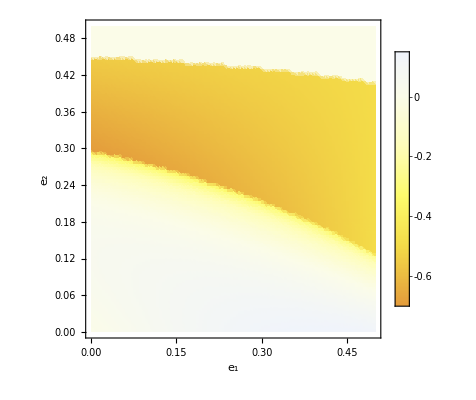

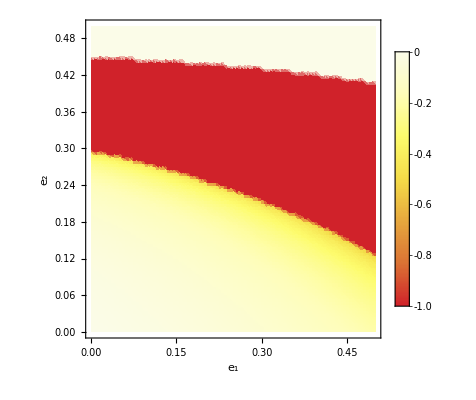

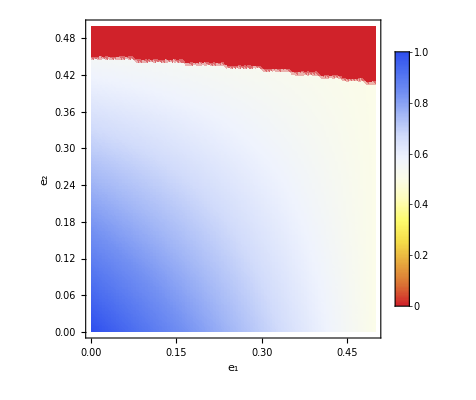

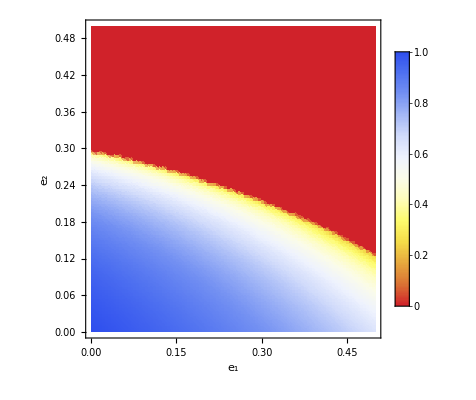

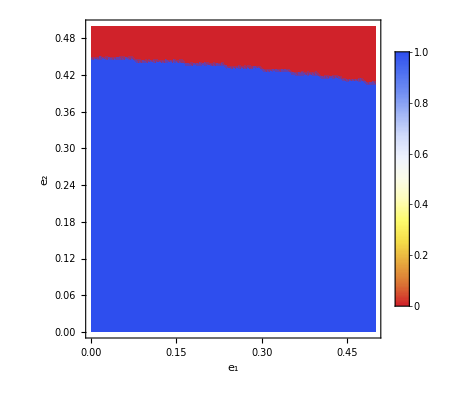

-Graphics-

```mathematica
Staying
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
Bayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg-gz[t])/.{x->x[t],y->y[t]})
};
nonBayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(e-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(ϵ-gz[t])/.{x->x[t],y->y[t]})
};
coopBayes=Array[m,{10201,3}];
zoutBayes=Array[m,{10201,3}];
coopnonBayes=Array[m,{10201,3}];
zoutnonBayes=Array[m,{10201,3}];
coop=Array[m,{10201,3}];
zout=Array[m,{10201,3}];
count = 1;
Do[
RBayes=NDSolve[Join[Evaluate[Bayessys/.{e1->i/200,e->j/200}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
RnonBayes=NDSolve[Join[Evaluate[nonBayessys/.{e1->i/200,e->j/200}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
coopBayes[[count]]= {i/200,j/200,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]};
zoutBayes[[count]]= {i/200,j/200,1-y[100000]/.RBayes[[1]]};
coopnonBayes[[count]]= {i/200,j/200,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]};
zoutnonBayes[[count]]= {i/200,j/200,1-y[100000]/.RnonBayes[[1]]};
coop[[count]]= {i/200,j/200,Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]]-Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]]};
zout[[count]]= {i/200,j/200,Evaluate[1-y[100000]/.RBayes[[1]]]-Evaluate[1-y[100000]/.RnonBayes[[1]]]};
count=count+1;
,{i,0,100},{j,0,100}];
ListDensityPlot[coop,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[zout,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[coopnonBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[coopBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[zoutnonBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[zoutBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
```

```mathematica
coopnonBayes
```

{{0,0,1.},{0,1/200,0.995},{0,1/100,0.99},{0,3/200,0.985},{0,1/50,0.98},{0,1/40,0.975},{0,3/100,0.97},{0,7/200,0.965},{0,1/25,0.96},10184,{1/2,93/200,0.465},{1/2,47/100,0.47},{1/2,19/40,0.475},{1/2,12/25,0.48},{1/2,97/200,0.485},{1/2,49/100,0.49},{1/2,99/200,0.495},{1/2,1/2,0.5}}
 |  |  |  |

```mathematica
Stern judging
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g+Qcb*(1-g)-gx[t],
gy'[t]==Qdg*g+Qdb*(1-g)-gy[t],
gz'[t]==Qcg*g+Qdb*(1-g)-gz[t]
};
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
Bayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg*g+Qcb*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg*g+Qdb*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg*g+Qdb*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
nonBayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(ϵ*g+(1-ϵ)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(e*g+(1-e)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(ϵ*g+(1-e)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
coopBayes=Array[m,{10201,3}];
zoutBayes=Array[m,{10201,3}];
coopnonBayes=Array[m,{10201,3}];
zoutnonBayes=Array[m,{10201,3}];
coop=Array[m,{10201,3}];
zout=Array[m,{10201,3}];
count = 1;
Do[
RBayes=NDSolve[Join[Evaluate[Bayessys/.{e1->i/200,e->j/200}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
RnonBayes=NDSolve[Join[Evaluate[nonBayessys/.{e1->i/200,e->j/200}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
coopBayes[[count]]= {i/200,j/200,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]};
zoutBayes[[count]]= {i/200,j/200,1-y[100000]/.RBayes[[1]]};
coopnonBayes[[count]]= {i/200,j/200,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]};
zoutnonBayes[[count]]= {i/200,j/200,1-y[100000]/.RnonBayes[[1]]};
coop[[count]]= {i/200,j/200,Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]]-Evaluate[(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]]};
zout[[count]]= {i/200,j/200,Evaluate[1-y[100000]/.RBayes[[1]]]-Evaluate[1-y[100000]/.RnonBayes[[1]]]};
count=count+1;
,{i,0,100},{j,0,100}];
ListDensityPlot[coop,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[zout,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,-1}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[coopnonBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[coopBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[zoutnonBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
ListDensityPlot[zoutBayes,PlotRange->Full,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0}]]&),PlotLegends->Automatic,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{"e_1","e_2"},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
```

judging Stern

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»